```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

#### Definiciones de

```mathematica
cSpeed=137.035999139;
nm=100./5.2918;
wp=0.48297106037599996;
gam=0.007244389509;
```

```mathematica
ϵDrude[ω_,ωp_,γ_]=1-ωp^2/(ω(ω+ⅈ γ));
```

```mathematica
II[l_,m_,i1_,i2_]:=If[l==m-2 || l==m-1,
0.,
If[l==m,
If[Mod[i2,2]==0,(-1.)^m Factorial2[2m-1]Beta[(i1+m+2)/2,(i2+1)/2],0],
1./(l-m)((2l-1)*II[l-1,m,i1,i2+1]-(l+m-1)II[l-2,m,i1,i2])
]
]
```

```mathematica
IM[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x,{x,-1,1}]
IU[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*1/(√(1-x^2)),{x,-1,1}]
IV[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x^2/(√(1-x^2)),{x,-1,1}]
IW[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x/(√(1-x^2)),{x,-1,1}]
```

```mathematica
llmax=11;
Timing[IMlist=Table[IM[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IUlist=Table[IU[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IVlist=Table[IV[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
IWlist=Table[IW[l1,l2,m1,m2],{l1,1,llmax},{l2,1,llmax},{m1,-l1,l1},{m2,-l2,l2}];
]//Quiet
```

{988.781,Null}

```mathematica
Export["Integrals/IMlist.mx",IMlist];
Export["Integrals/IUlist.mx",IUlist];
Export["Integrals/IVlist.mx",IVlist];
Export["Integrals/IWlist.mx",IWlist];
```

```mathematica
llmax=11;
Timing[IIlist=Table[II[l,m,j, l-j],{l,1,llmax},{m,0,l},{j,m,l}];
]//Quiet
```

{0.140625,Null}

```mathematica
Export["Integrals/IIlist.mx",IIlist];
```

```mathematica
αlm[l_,m_]=√((2l+1.)/(4π)((l-m)!)/((l+m)!));
gamma[betav_]=1./(√(1-betav^2));
AA[l_,m_,betav_]:=If[m<0,
(-1)^Abs[m] AA[l,Abs[m],betav],
1./betav^(l+1)∑_(j=m)^l (ⅈ^(l-j)Factorial2[2l+1]αlm[l,m])/(gamma[betav]^j 2^j Factorial[(j-m)/2]Factorial[(j+m)/2])IIlist[[l,m+1,j+1-m]]
](*II[l,m,j,l-j]*)
BB[l_,m_,betav_]:=AA[l,m+1,betav] √((l+m+1)(l-m))-AA[l,m-1,betav] √((l-m+1)(l+m))
```

```mathematica
IMlist=Import["Integrals/IMlist.mx"];
IUlist=Import["Integrals/IUlist.mx"];
IVlist=Import["Integrals/IVlist.mx"];
IWlist=Import["Integrals/IWlist.mx"];
IIlist=Import["Integrals/IIlist.mx"];
```

```mathematica
j[l_,z_]=SphericalBesselJ[l,z];
dj[l_,z_]=j[l,z]+0.5*z*(j[l-1,z]-j[l+1,z]-j[l,z]/z);
h[l_,z_]=ⅈ SphericalHankelH1[l,z];
dh[l_,z_]=h[l,z]+0.5*z*(h[l-1,z]-h[l+1,z]-h[l,z]/z);
```

```mathematica
z[i_,l_,w_,r_]:={h[l,w*r/cSpeed],j[l,w*r/cSpeed]}[[i+1]];
f[i_,l_,w_,r_]:={(l+1)h[l,w*r/cSpeed]/(w*r/cSpeed)-h[l+1,w*r/cSpeed],(l+1)j[l,w*r/cSpeed]/(w*r/cSpeed)-j[l+1,w*r/cSpeed]}[[i+1]];
```

```mathematica
tEl[a_,w_, ϵ_,l_]:=(-j[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]+ϵ[w]j[l,w a √ϵ[w]/cSpeed]*dj[l,w a/cSpeed])/(h[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]-ϵ[w]j[l,w a √ϵ[w]/cSpeed]*dh[l,w a/cSpeed])
tMl[a_,w_, ϵ_,l_]:=(j[l,w a√ϵ[w]/cSpeed]*dj[l,w a/cSpeed]-j[l,w a /cSpeed]*dj[l,w a√ϵ[w]/cSpeed])/(h[l,w a/cSpeed]*dj[l,w a√ϵ[w]/cSpeed]-j[l,w a √ϵ[w]/cSpeed]*dh[l,w a/cSpeed])
```

```mathematica
ψE[l_,m_,w_,b_,betav_]=(-2π ⅈ^(l-1)w)/(cSpeed^2 gamma[betav])*BB[l,m,betav]/(l(l+1))BesselK[m,(w*b)/(betav*cSpeed*gamma[betav])];
ψM[l_,m_,w_,b_,betav_]=(-4π ⅈ^(l-1)w*betav)/(cSpeed^2 gamma[betav])*(m*AA[l,m,betav])/(l(l+1))BesselK[m,(w*b)/(betav*cSpeed*gamma[betav])];
```

```mathematica
DE[l_,m_,w_,b_,betav_]=ⅈ^l*αlm[l,m]*ψE[l,m,w,b,betav];
CM[l_,m_,w_,b_,betav_]=ⅈ^l*αlm[l,m]*ψM[l,m,w,b,betav];
```

#### Pruebas de funciones

```mathematica
ll=1;mm=1;betavv=0.7;jj=mm;ii1=jj;ii2=ll-jj;
AA[ll,mm,betavv]
BB[ll,mm,betavv]
```

-1.00707

0.-2.82036 ⅈ

```mathematica
ll=3;mm=0;jj=2;
IIlist[[ll,mm+1,jj-mm+1]]
II[ll,mm,jj,ll-jj]
```

-0.114286

-0.114286

```mathematica
IVlist[[1,1,-1+1+1]]
```

{0.0981748,0.,-0.19635}

```mathematica
aa=1.0*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];ll=1;
tEl[aa,ww,ϵϵ,ll]
```

3.49214×10^-17+8.8282×10^-23 ⅈ

```mathematica
ϵDrude[1,wp,gam]
```

0.766751+0.00168975 ⅈ

```mathematica
ll1=1;ll2=1;mm1=-1;mm2=-1;
IVlist[[ll1,ll2,mm1+ll1+1,mm2+ll2+1]]
IV[ll1,ll2,mm1,mm2]
```

0.0981748

0.0981748

#### IErtx

```mathematica
ll1=1;mm1=-1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
ⅈ*(mm1-mm2)*(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
ⅈ*(mm1-mm2)*(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll2,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll2,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
```

5.99178×10^-13-4.1775×10^-29 ⅈ

-5.3074×10^-13+0. ⅈ

3.98753×10^-13+1.00805×10^-18 ⅈ

-7.97506×10^-13+2.01611×10^-18 ⅈ

```mathematica
aa
```

18.8972

```mathematica
1i*(dm1-dm2)*(-tEl[l1-1]*DE[l1-1][m1+l1]*conj(tEl[l2-1]*DE[l2-1][m2+l2]*dz[0][l2-1])*(df[0][l1-1]/(k0*r))*dl2*(dl2+1.)*((dl1+1.)*IW1-(dl1-dm1+1.)*IU2)-tMl[l1-1]*CM[l1-1][m1+l1]*conj(tEl[l2-1]*DE[l2-1][m2+l2]*dz[0][l2-1])*(dz[0][l1-1]/(k0*r))*dm1*dl2*(dl2+1.)*IU1);
```

#### IErty

```mathematica
ll1=1;mm1=-1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=0.00016350137266446518;ϵϵ[w_]=ϵDrude[w,wp,gam];
(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
(-DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IW[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IU[ll1+1,ll2,mm1,mm2])-CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IU[ll1,ll2,mm1,mm2])
```

4.47722×10^-26+2.93481×10^-12 ⅈ

0.-2.5996×10^-12 ⅈ

-2.9753×10^-17+1.95312×10^-12 ⅈ

-5.9506×10^-17-3.90624×10^-12 ⅈ

```mathematica
(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]]);
```

Part::pkspec1: The expression l1 cannot be used as a part specification.

Part::pkspec1: The expression 1+l1 cannot be used as a part specification.

Part::pkspec1: The expression l1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

#### IHrty

```mathematica
IHrty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### IErfy

```mathematica
ll1=1;mm1=1;ll2=1;mm2=0;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
-(mm1-mm2)*(tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(tMl[aa,ww,ϵϵ,ll1]*CM[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*z[0,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+tEl[aa,ww,ϵϵ,ll1]*DE[ll1,mm1,ww,bb, betavv]*Conjugate[DE[ll2,mm2,ww,bb, betavv]*z[1,ll2,ww,rr]]*f[0,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
-(mm1-mm2)*(CM[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*z[1,ll1,ww,rr]/(ww*rr/cSpeed)*ll2(ll2+1)((ll1+1)*IV[ll1,ll2,mm1,mm2]-(ll1-mm1+1)IW[ll1+1,ll2,mm1,mm2])+DE[ll1,mm1,ww,bb, betavv]*Conjugate[tEl[aa,ww,ϵϵ,ll2]*DE[ll2,mm2,ww,bb, betavv]*z[0,ll2,ww,rr]]*f[1,ll1,ww,rr]/(ww*rr/cSpeed)*mm1*ll2*(ll2+1)IW[ll1,ll2,mm1,mm2])
```

3.02416×10^-18+3.30315×10^-13 ⅈ

```mathematica
-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]]);
```

Part::pkspec1: The expression l1 cannot be used as a part specification.

Part::pkspec1: The expression 1+l1 cannot be used as a part specification.

Part::pkspec1: The expression l1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
IErfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### IHrfy

```mathematica
IHrfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### Fields

```mathematica
IErty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])-CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IHrty[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])+(-CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IWlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IUlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IUlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IErfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[DE[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(CM[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+DE[l1,m1,w,b, betav]*Conjugate[tEl[a,w,ϵ,l2]*DE[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

```mathematica
IHrfy[l1_,l2_,m1_,m2_,w_,a_, r_,b_, betav_, ϵ_]:=Re[-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l1]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-tEl[a,w,ϵ,l1]*DE[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*z[0,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+tMl[a,w,ϵ,l1]*CM[l1,m1,w,b, betav]*Conjugate[CM[l2,m2,w,b, betav]*z[1,l2,w,r]]*f[0,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])-(m1-m2)*(-DE[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*z[1,l1,w,r]/(w*r/cSpeed)*l2(l2+1)((l1+1)*IVlist[[l1,l2,m1+l1+1,m2+l2+1]]-(l1-m1+1)IWlist[[l1+1,l2,m1+l1+1+1,m2+l2+1]])+CM[l1,m1,w,b, betav]*Conjugate[tMl[a,w,ϵ,l2]*CM[l2,m2,w,b, betav]*z[0,l2,w,r]]*f[1,l1,w,r]/(w*r/cSpeed)*m1*l2*(l2+1)IWlist[[l1,l2,m1+l1+1,m2+l2+1]])]
```

#### Rest

```mathematica
ClearAll[m1,m2]
```

```mathematica
dldwEy[w_,lmax_,a_,b_,r_,betav_, ϵ_]:=Sum[If[m1==m2+1||m2==m1+1,1/(4π)r^3(IErty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IErfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0],{l1,1,lmax},{l2,1,lmax},{m1,-l1,l1},{m2,-l2,l2}]
dldwHy[w_,lmax_,a_,b_,r_,betav_, ϵ_]:=Sum[If[m1==m2+1||m2==m1+1,1/(4π)r^3(IHrty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IHrfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0],{l1,1,lmax},{l2,1,lmax},{m1,-l1,l1},{m2,-l2,l2}]
```

```mathematica
dldwmmEy[w_,l1_,l2_,a_,b_,r_,betav_, ϵ_]:=1/(4π)*r^3*∑_(m1=-l1)^l1 (∑_(m2=-l2)^l2 If[m1==m2+1||m2==m1+1,(IErty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IErfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0])
dldwmmHy[w_,l1_, l2_,a_,b_,r_,betav_, ϵ_]:=1/(4π)*r^3*∑_(m1=-l1)^l1 (∑_(m2=-l2)^l2 If[m1==m2+1||m2==m1+1,(IHrty[l1,l2,m1,m2,w,a, r,b, betav, ϵ]-IHrfy[l1,l2,m1,m2,w,a, r,b, betav, ϵ]),0])
```

```mathematica
llmax=1;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.05*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
dldwEy[ww,llmax,aa,bb,rr,betavv,ϵϵ]
dldwHy[ww,llmax,aa,bb,rr,betavv,ϵϵ]
```

-1.72859×10^-14

1.28246×10^-18

```mathematica
llmax=4;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
NIntegrate[ dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-1.2826×10^-6

1.97419×10^190

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-0.000110708

```mathematica
llmax=2;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]+NIntegrate[ dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-0.00011593

```mathematica
llmax=3;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]+NIntegrate[ dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet
```

-0.00011611

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH2= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE2= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=3;betavv=0.7;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH3= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE3= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

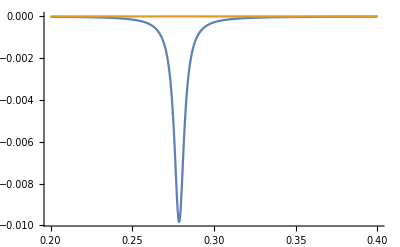

```mathematica
ListPlot[{DLDWYE, DLDWYH}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

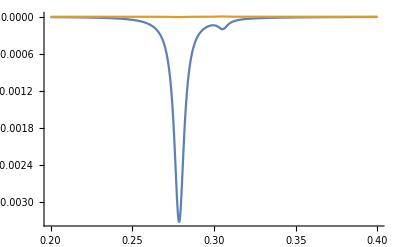

```mathematica
ListPlot[{DLDWYE2, DLDWYH2}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

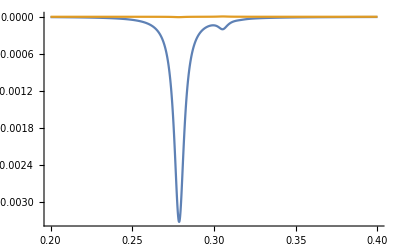

```mathematica
ListPlot[{DLDWYE3, DLDWYH3}, PlotRange->All, Joined->True, InterpolationOrder->2]
```

```mathematica
ll1=1;ll2=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYMM1H= ParallelTable[{ω,dldwmmHy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYMM1E= ParallelTable[{ω,dldwmmEy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
ll1=2;ll2=2;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYMM2H= ParallelTable[{ω,dldwmmHy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYMM2E= ParallelTable[{ω,dldwmmEy[ω,ll1,ll2,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
DLDWYH2= ParallelTable[{ω,dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
DLDWYE2= ParallelTable[{ω,dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ]},{ω,0.2,0.4, 0.0005}]//Quiet;
```

```mathematica
DLDWYMME;
```

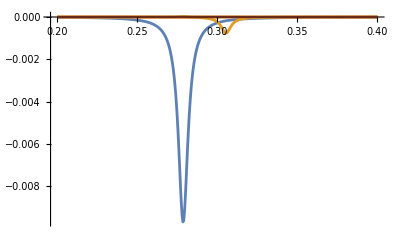

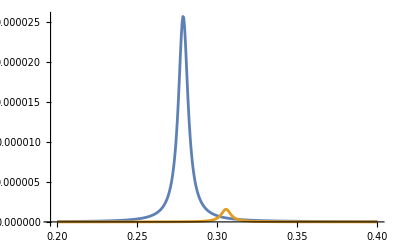

```mathematica
ListPlot[{DLDWYMM1E, DLDWYMM2E,DLDWYMM1H, DLDWYMM2H}, Joined->True, PlotRange->All]
ListPlot[{DLDWYMM1H, DLDWYMM2H}, Joined->True, PlotRange->All]
```

```mathematica
wp/√(5/2)
```

0.305458

```mathematica
Plot[]
```

$Aborted

```mathematica
IW[ll1,ll2,mm1,mm2]
IW[ll1+1,ll2,mm1,mm2]
IU[ll1,ll2,mm1,mm2]
IV[ll1,ll2,mm1,mm2]
```

0.333333

0.

0.

0.

```mathematica
dldwy[0]+=(1./(4.*Pi))*r*r*r*((IErty[2]-IErfy[2]).real()+(IErty[3]-IErfy[3]).real());
```

```mathematica
llmax=2;betavv=0.7;aa=1.0*nm;bb=20.0*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];
"l1=2  l2=1  m1=-2  m2=-1";
ll1=2;ll2=1;mm1=-1;mm2=-1;
IErfy[ll1,ll2,mm1,mm2,w,aa,rr,bb,betavv,ϵϵ]
```

0.

```mathematica
llmax=1;betavv=0.5;aa=1.0*nm;bb=3.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=30;
Lysmallb=ParallelTable[{b,10^4 NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,1,10,(10.-1)/nn}]
```

{{1.,-7.2021},{1.3,-5.00738},{1.6,-3.72435},{1.9,-2.89563},{2.2,-2.3231},{2.5,-1.9079},{2.8,-1.59555},{3.1,-1.35375},{3.4,-1.1622},{3.7,-1.00758},{4.,-0.880776},{4.3,-0.775395},{4.6,-0.686809},{4.9,-0.611601},{5.2,-0.547196},{5.5,-0.49162},{5.8,-0.443339},{6.1,-0.401141},{6.4,-0.364058},{6.7,-0.331312},{7.,-0.302268},{7.3,-0.276402},{7.6,-0.253282},{7.9,-0.232546},{8.2,-0.213892},{8.5,-0.197061},{8.8,-0.181836},{9.1,-0.168029},{9.4,-0.155479},{9.7,-0.144049},{10.,-0.133617}}

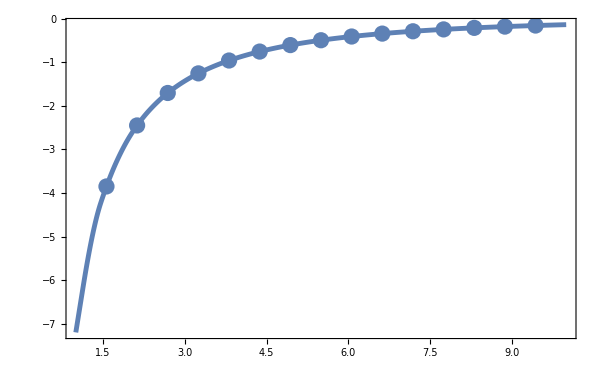

```mathematica
ListLinePlot[
Lysmallb,
InterpolationOrder->2,
PlotRange->{All,All},
Frame->True,
Mesh->True,
FrameLabel->{MaTeX["b \\, [\\text{nm}]",FontSize->25],MaTeX["\\Delta L \\times 10^{-4} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->AbsoluteThickness[3.5],
PlotLegends->Placed[LineLegend[MaTeX[{"\\, \\text{Drude Al}","\\, \\text{Prolate}","\\, \\text{Oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["a\\text{=1nm}, v=\\text{0.5}c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.7,0.32}],
ImageSize->600]
```

```mathematica
llmax=1;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=20;
Lysmallb1=ParallelTable[{b,10^3 NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,5.5,10,(10-5.5)/nn}]
```

{{5.5,-3.14431},{5.725,-2.92818},{5.95,-2.73219},{6.175,-2.5539},{6.4,-2.39122},{6.625,-2.24238},{6.85,-2.10584},{7.075,-1.98029},{7.3,-1.86458},{7.525,-1.75773},{7.75,-1.65885},{7.975,-1.56719},{8.2,-1.48207},{8.425,-1.40289},{8.65,-1.32913},{8.875,-1.26031},{9.1,-1.19601},{9.325,-1.13585},{9.55,-1.07951},{9.775,-1.02667},{10.,-0.977065}}

```mathematica
llmax=2;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=20;
Lysmallb2=ParallelTable[{b,10^3 NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0, 40 }]//Quiet},{b,5.5,10,(10-5.5)/nn}]
```

{{5.5,-5.61579},{5.725,-5.12133},{5.95,-4.68705},{6.175,-4.30354},{6.4,-3.96314},{6.625,-3.65961},{6.85,-3.3878},{7.075,-3.14344},{7.3,-2.92294},{7.525,-2.72329},{7.75,-2.54197},{7.975,-2.37679},{8.2,-2.2259},{8.425,-2.08772},{8.65,-1.96086},{8.875,-1.84415},{9.1,-1.73652},{9.325,-1.63709},{9.55,-1.54505},{9.775,-1.4597},{10.,-1.38042}}

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=20;
Lysmallb3=ParallelTable[{b,10^3 NIntegrate[ dldwEy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ]+dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0.0001, 40}]},{b,5.5,10,(10-5.5)/nn}]//Quiet
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00378057 and 0.0000608959 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.0049405 and 0.0000800689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00297796 and 0.0000473943 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00671487 and 0.000108289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00450193 and 0.0000728786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00348166 and 0.0000558834 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.0027645 and 0.0000437877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00603058 and 0.0000975787 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00321571 and 0.0000514064 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00257208 and 0.0000405358 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00411827 and 0.0000665276 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00544527 and 0.0000882437 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00196453 and 0.0000303009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00173353 and 0.000026442 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00239799 and 0.0000375957 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00153786 and 0.0000231982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00163175 and 0.0000247514 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.0018441 and 0.0000282859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00223994 and 0.0000349302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.00145106 and 0.0000217686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.322517}. NIntegrate obtained -0.002096 and 0.0000325078 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{5.5,-6.71487},{5.725,-6.03058},{5.95,-5.44527},{6.175,-4.9405},{6.4,-4.50193},{6.625,-4.11827},{6.85,-3.78057},{7.075,-3.48166},{7.3,-3.21571},{7.525,-2.97796},{7.75,-2.7645},{7.975,-2.57208},{8.2,-2.39799},{8.425,-2.23994},{8.65,-2.096},{8.875,-1.96453},{9.1,-1.8441},{9.325,-1.73353},{9.55,-1.63175},{9.775,-1.53786},{10.,-1.45106}}

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
Table[dldwHy[ω,llmax,aa,b*nm,rr,betavv,ϵϵ],{ω,0.1, 6},{b,5.5,10,(10-5.5)/nn}]
```

{{-0.000159516,-0.000121399,-0.0000945911,-0.0000751776,-0.0000607655,-0.0000498355,-0.0000413913,-0.0000347612,-0.0000294805,-0.0000252209,-0.0000217459},{-1.74418×10^-6,-1.27722×10^-6,-9.45811×10^-7,-7.07192×10^-7,-5.33221×10^-7,-4.04997×10^-7,-3.09588×10^-7,-2.38003×10^-7,-1.83895×10^-7,-1.42729×10^-7,-1.11228×10^-7},{-2.21573×10^-6,-1.38312×10^-6,-8.73931×10^-7,-5.57797×10^-7,-3.59061×10^-7,-2.32814×10^-7,-1.51903×10^-7,-9.96513×10^-8,-6.56859×10^-8,-4.34802×10^-8,-2.88895×10^-8},{-9.70257×10^-7,-5.17146×10^-7,-2.78789×10^-7,-1.51716×10^-7,-8.32202×10^-8,-4.59575×10^-8,-2.55274×10^-8,-1.42512×10^-8,-7.99133×10^-9,-4.49869×10^-9,-2.54136×10^-9},{-2.71507×10^-7,-1.23745×10^-7,-5.69691×10^-8,-2.64477×10^-8,-1.23654×10^-8,-5.81645×10^-9,-2.75029×10^-9,-1.30642×10^-9,-6.23063×10^-10,-2.98214×10^-10,-1.43188×10^-10},{-4.19543×10^-8,-1.63517×10^-8,-6.42859×10^-9,-2.54585×10^-9,-1.01448×10^-9,-4.0642×10^-10,-1.63577×10^-10,-6.6106×10^-11,-2.68118×10^-11,-1.09095×10^-11,-4.4518×10^-12}}

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
NIntegrate[ dldwEy[ω,llmax,aa,bb,rr,betavv,ϵϵ],{ω,0, 10 }]//Quiet
NIntegrate[dldwHy[ω,llmax-1,aa,bb,rr,betavv,ϵϵ],{ω,0, 10 }]//Quiet
```

-0.00636492

-0.000277169

```mathematica
llmax=3;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=0.27133085101382903;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
dldwEy[ww,llmax,aa,bb,rr,betavv,ϵϵ]//Quiet
dldwHy[ww,llmax,aa,bb,rr,betavv,ϵϵ]//Quiet
```

-0.148279

-0.00598769

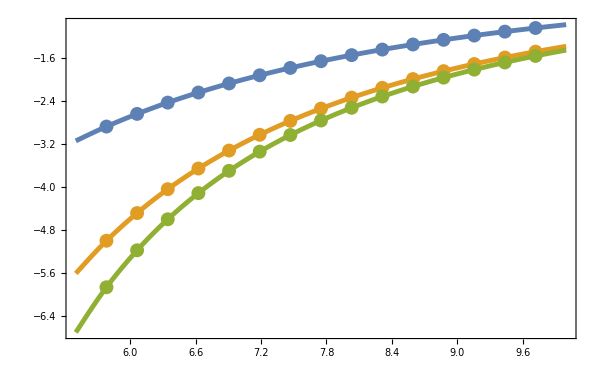

```mathematica
ListLinePlot[
{Lysmallb1, Lysmallb2, Lysmallb3},
InterpolationOrder->2,
PlotRange->{All,All},
Frame->True,
Mesh->True,
FrameLabel->{MaTeX["b \\, [\\text{nm}]",FontSize->25],MaTeX["\\Delta L \\times 10^{-3} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->AbsoluteThickness[3.5],
PlotLegends->Placed[LineLegend[MaTeX[{"\\, \\ell=1","\\, \\ell =2","\\, \\ell=3","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Drude-Al}, \\, a\\text{=5nm}, v=\\text{0.6 c}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.65,0.22}],
ImageSize->600]
```

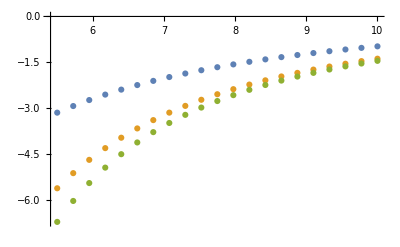

```mathematica
ListPlot[{Lysmallb1, Lysmallb2, Lysmallb3}]
```

```mathematica
SphericalBesselJ[1,x]
```

SphericalBesselJ[1,x]

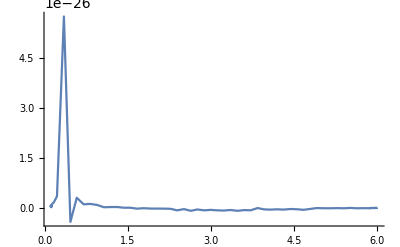

```mathematica
llmax=3;mm1=-llmax+6;mm2=-llmax+6;betavv=0.6;aa=5.0*nm;bb=5.5*nm;rr=aa+0.1*nm;ww=2.7133085101382903*10^-5;ϵϵ[w_]=ϵDrude[w,wp,gam];nn=10;
Plot[Sum[IHrty[llmax,l2,m1,m2,w,aa, rr,bb, betavv, ϵϵ]-IHrfy[llmax,llmax,mm1,mm2,w,aa, rr,bb, betavv, ϵϵ],{l2,1,3},{m1,-llmax,llmax},{m2,-l2,l2}],{w,0.1,6}, PlotRange->All]
```

```mathematica
IHrty[llmax,1,,m2,w,aa, rr,bb, betavv, ϵϵ]
```

```mathematica
αlm[4,1]
```

0.189235

```mathematica
162*30
```

4860

```mathematica
16/130.
```

0.123077